# Loss compensation function

Suppose there is a corporation with an initial capital of 1.

This company loses “X” in a bet, thus reducing its net worth to 1 - X.

In order to regain its initial capital of 1, it is necessary to earn Y in order to make up a final net worth of (1 - x) * (1 + x + y). The first parcel regards to the loser bet, and the second to the supposed winner bet.

Y is thus

```mathematica
Solve[-Log[1-x]==Log[1+x+y]&&0≤x<1,y]
```

{{y→ConditionalExpression[-x^2/(-1+x),0≤x<1]}}

Below we see the excess y==-x^2/(-1+x) to be compensated

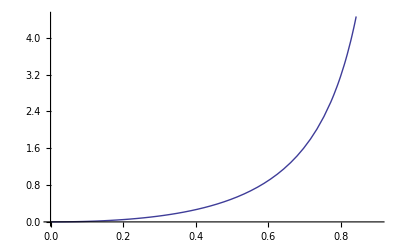

```mathematica
Plot[x^2/(1-x),{x,0,0.9}]
```